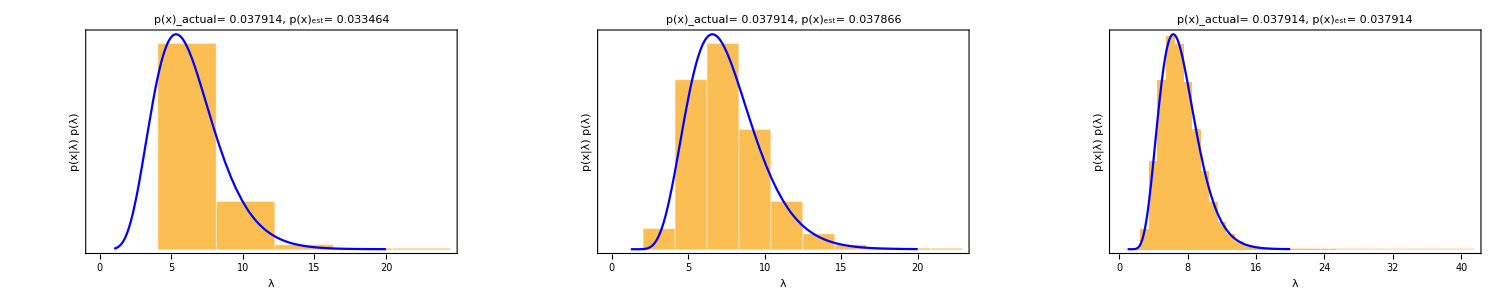

```mathematica
SetDirectory[NotebookDirectory[]];
fPrior[λ_]:=PDF[LogNormalDistribution[1,1],λ]
data={7};
fLikelihood[λ_,lData__]:=Likelihood[PoissonDistribution[λ],lData]
aDenominator=NIntegrate[fLikelihood[λ,data]fPrior[λ],{λ,0,∞}];
fPosteriorUnnormalised[λ_,lData_]:=fLikelihood[λ,lData] fPrior[λ]
fPosterior[λ_,lData_,aDenominator_]:=fLikelihood[λ,lData] fPrior[λ]/aDenominator
lPosteriorUnnormalised=Table[If[i==0,{2,0},{2,fPosteriorUnnormalised[i,data]}],{i,0,20,2}];
g2=Show[RectangleChart[lPosteriorUnnormalised,ChartLabels->Table[i,{i,0,20,2}],Frame->{True,True,False,False},FrameTicks->{True,None},BaseStyle->{FontSize->14},FrameLabel->{"λ","p(x|λ) p(λ)"},PlotLabel->StringJoin["p(x)_actual= ",ToString@NumberForm[aDenominator,{6,6}],", p(x)_est= ",ToString@NumberForm[N@Total@lPosteriorUnnormalised[[All,2]]2,{6,6}]]],Plot[fPosteriorUnnormalised[λ-1.25,data],{λ,1.25,20},PlotRange->Full,PlotStyle->Blue]];
lPosteriorUnnormalised=Table[If[i==0,0,fPosteriorUnnormalised[i,data]],{i,0,40,1}];
g3=Show[BarChart[lPosteriorUnnormalised,Frame->{True,True,None,None},FrameTicks->{True,None},BaseStyle->{FontSize->14},FrameLabel->{"λ","p(x|λ) p(λ)"},PlotLabel->StringJoin["p(x)_actual= ",ToString@NumberForm[aDenominator,{6,6}],", p(x)_est= ",ToString@NumberForm[N@Total@lPosteriorUnnormalised,{6,6}]]],Plot[fPosteriorUnnormalised[λ-1,data],{λ,1,20},PlotStyle->Blue]];
lPosteriorUnnormalised1=Table[If[i==0,0,fPosteriorUnnormalised[i+2,data]],{i,0,20,4}];
g1=Show[RectangleChart[Thread[{4,lPosteriorUnnormalised1}],Frame->{True,True,None,None},FrameTicks->{True,None},BaseStyle->{FontSize->14},FrameLabel->{"λ","p(x|λ) p(λ)"},PlotLabel->StringJoin["p(x)_actual= ",ToString@NumberForm[aDenominator,{6,6}],", p(x)_est= ",ToString@NumberForm[N@Total@lPosteriorUnnormalised1 4,{6,6}]]],Plot[fPosteriorUnnormalised[λ,data],{λ,1,20},PlotStyle->Blue]];
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1500]
```

```mathematica
Export["MCMC_quadratureBSE.pdf",gFinal]
```

MCMC_quadratureBSE.pdf

```mathematica
10^20
```

100000000000000000000